## Hopf Bifurcation in the Averaged System

Again, consider the averaged system without π in the frequency term:

```mathematica
Subscript[s, x]'=ϵ(-Subscript[s, x]+√(Subscript[a, 1]+Subscript[b, 1] Subscript[s, x]-Subscript[c, 1] Subscript[s, y]))/Subscript[μ, x],
Subscript[s, y']=ϵ(-Subscript[s, y]+√(Subscript[a, 2]+Subscript[b, 2] Subscript[s, x]-Subscript[c, 2] Subscript[s, y]))/Subscript[μ, y].
```

In the log, we calculate the trace and determinant for the Jacobian:

```mathematica
Trace[J]= 1/(2 √w)v-2,
Det[J]=1/(2 √w) v-(b c)/(2w Subscript[μ, x] Subscript[μ, y])+1,
```

where w=a+b s_x-c s_y and v=(c/μ_y-b/μ_x) To find the Hopf bifurcation, we require

```mathematica
0=1/(2 √w) v-2,
(v (v-16 √w)+(8 b c)/(Subscript[μ, x] Subscript[μ, y]))/(4 w)<0,
```

where the last line is the term under the radical. Together, we derive a single inequality,

```mathematica
(b c)/(Subscript[μ, x] Subscript[μ, y])<w=a + b s̄-c s̄.
```

Altogether, we require

```mathematica
0<a + b s̄-c s̄-(b c)/(Subscript[μ, x] Subscript[μ, y]),
0 < a + b s̄-c s̄,
(b s̄)/Subscript[μ, x]-(c s̄)/Subscript[μ, y]-4 √(a+b-c)=0
```

We perform these calculations below.

```mathematica
(* given mux,muy,b,c, find a *)
sbarv[a_,b_,c_]:=1/2 ((b-c)+±√((b-c)^2+4 a))
aval[mx_,my_,b_,c_,sbar_]:=(c mx-b my)^2/(16 mx^2 my^2)+(-b+c) sbar;
```

```mathematica
Solve[a==(c mx-b my)^2/(16 mx^2 my^2)+(-b+c) 1/2 ((b-c)+√((b-c)^2+4 a)),a]
```

{{a→(c^2 mx^2-2 b c mx my-4 b c mx^2 my+4 c^2 mx^2 my+b^2 my^2+4 b^2 mx my^2-4 b c mx my^2)/(16 mx^2 my^2)},{a→(c^2 mx^2-2 b c mx my+4 b c mx^2 my-4 c^2 mx^2 my+b^2 my^2-4 b^2 mx my^2+4 b c mx my^2)/(16 mx^2 my^2)}}

```mathematica
aval[mx_,my_,b_,c_]:=(c^2 mx^2-2 b c mx my-4 b c mx^2 my+4 c^2 mx^2 my+b^2 my^2+4 b^2 mx my^2-4 b c mx my^2)/(16 mx^2 my^2);
av =aval[1,5,5,1]
sbarv[av,5,10]
```

156/25

1/2 (-5+±(√1249)/5)

```mathematica
3
```

```mathematica
a/.%92
```

{(c^2 mx^2-2 b c mx my-4 b c mx^2 my+4 c^2 mx^2 my+b^2 my^2+4 b^2 mx my^2-4 b c mx my^2)/(16 mx^2 my^2),(c^2 mx^2-2 b c mx my+4 b c mx^2 my-4 c^2 mx^2 my+b^2 my^2-4 b^2 mx my^2+4 b c mx my^2)/(16 mx^2 my^2)}

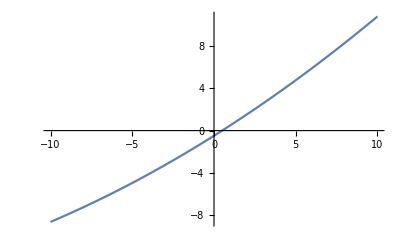

```mathematica
(* give mux,muy,b, find relationship between a and c*)
Plot[1/16 (c (16+c/my^2)+(b (b my-2 mx (c+8 mx my)))/(mx^2 my))/.mx->1/.my->2/.b->.5,{c,-10,10}]
```

These calculations help determine the existence of hopf bifurcations, but the trouble now is to determine the criticality of the Hopf bifurcation.

```mathematica
aa=156/25;bb=5;cc=1;
xx=(a+b sbarr + c sbarr)^(-1/2);
fx=c/2 xx;
fxx=-c^2/4 xx^3;
fxxx=(3 c^3)/8 xx^5;
fxy=-(b c)/4 xx^3;
fxyy=(3 b^2 c)/8 xx^5;
fxxy=(3 c^2 b)/8 xx^5;
fy=b/2 xx;
fyy=-b^2/4 xx^3;
fyyy=(3 b^3)/8 xx^5;
gxx=fxx;
gxy=fxy;
gxxy=fxxy;
gy=fy;
gyy=fyy;
gyyy=fyyy;
FullSimplify[1/16(fxxx+fxyy+gxxy+gyyy)-1/16(fxy(fxx+fyy)-gxy(gxx+gyy)-fxx gxx + fyy gyy)/.a->aa/.b->bb/.c->cc]
```

-39/(16 (156/25+6 sbarr)^3)+117/(32 (156/25+6 sbarr)^(5/2))